λ^2/(1-λ^2)

```mathematica
(Sum[(λ^(2(n+m))),{n,0,∞},{m,0,∞}])^2(1-λ^2)^4
```

((1-λ^2)^4)/((-1+λ^2)^4)

```mathematica
FullSimplify[(Sum[(λ^(2(n+m))),{n,0,∞},{m,0,∞}])^2(1-λ^2)^4 ,Assumptions->{λ∈Reals}]
```

1

```mathematica
p1=Simplify[(1-λ^2)^2 Sum[(λ^(n+1)) ,{n,0,∞}]^2]
```

λ^2 (1+λ)^2

```mathematica
p2=Simplify[(1-λ^2)^2 Sum[(λ^(n+2)) ,{n,0,∞}]^2]
```

λ^4 (1+λ)^2

```mathematica
px=Simplify[(1-λ^2)^2 Sum[(λ^(n+x)) ,{n,0,∞}]^2]
```

λ^(2 x) (1+λ)^2

```mathematica
(2p2)/(p1+2p2)^2
```

```mathematica
g2simple=(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)
```

(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)

```mathematica
g2simple/.{λ->0.01}
```

1.95981

```mathematica
{λ^2/(1-λ^2),g2simple}/.{λ->Abs[lambdaGivenN[0.0001]]}
```

{0.0001,1.95981}

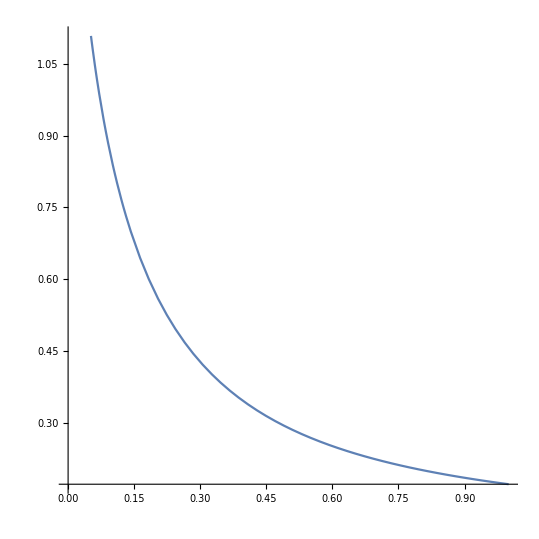

```mathematica
Plot[g2simple/.{λ->Abs[lambdaGivenN[x]]},{x,1,10^-4},AspectRatio->1]
```

```mathematica
g2full=Sum[n(n-1)(px/.{x->n}),{n,0,∞}]/Sum[n(px/.{x->n}),{n,0,∞}]^2
```

-(2 (-1+λ))/(1+λ)

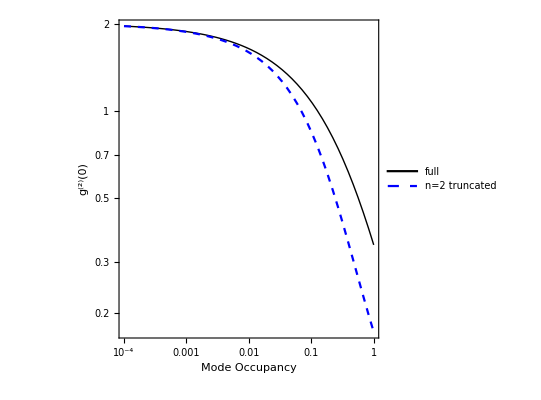

```mathematica
LogLogPlot[{g2full/.{λ->Abs[lambdaGivenN[x]]},g2simple/.{λ->Abs[lambdaGivenN[x]]}},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"full","n=2 truncated"},Center],PlotStyle->{{Black,Thick},{Blue,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","g^(2)(0)"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

```mathematica
SameQ[FullSimplify[-(2 (-1+λ))/(1+λ)],FullSimplify[(2 (1-λ))/(1+λ)]]
```

True

```mathematica
lambdaGivenN=InverseFunction[(#)^2/(1-(#)^2)&]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-(√#1)/(√(1+#1))&

```mathematica
a=Abs[]
λ^2/(1-λ^2)/.λ->a
```

0.031607

0.001

```mathematica
λ^2/(1-λ^2)/.{λ->0.02}
```

0.00040016

```mathematica
Limit[(2p2)/(p1+2p2)^2,λ->0]
```

2

```mathematica
Simplify[ Sum[(√(λ^n Factorial[n])√(1/(λ+1)(λ/(λ+1))^n))^2,{n,0,∞},{m,0,∞}]]
```

∑_(n=0)^∞ ∑_(m=0)^∞ (λ^n (λ/(1+λ))^n n!)/(1+λ)

```mathematica
p1=Simplify[ Sum[(√(1/(λ+1)(λ/(λ+1))^1)√(1/(λ+1)(λ/(λ+1))^n))^2,{n,0,∞}]]
```

λ/(1+λ)^2

```mathematica
p2=Simplify[ Sum[(√(1/(λ+1)(λ/(λ+1))^2)√(1/(λ+1)(λ/(λ+1))^n))^2,{n,0,∞}]]
```

λ^2/(1+λ)^3

```mathematica
p2/p1^2
```

1+λ

```mathematica
Factorial[X-N]
```

(-N+X)!

```mathematica
FullSimplify[1/(Factorial[m]Factorial[n])Factorial[m+n],Assumptions->{n>0,m>0}]
```

((m+n)!)/(m! n!)

```mathematica
Factorial[0]
```

1

## Finding Coincidences

Find the noncoincident output state probability

```mathematica
(1-λ^2)Sum[λ^(m+n)1/(Factorial[m]Factorial[n])(1/2)^(m+n)Sum[i^(j+k+a+b)e^(i ϕ(j-k+a-b))Binomial[n,j]Binomial[m,k]Binomial[n,a]Binomial[m,b] √(Factorial[m+n-j-k]Factorial[j+k])√(Factorial[m+n-a-b]Factorial[a+b])KroneckerDelta[m+n-j-k]KroneckerDelta[j+k-X]KroneckerDelta[m+n-a-b]KroneckerDelta[a+b-X] ,{j,0,n},{k,0,m},{a,0,n},{b,0,m}],{m,0,∞},{n,0,∞}]
```

$Aborted

```mathematica
innersum=FullSimplify[(FullSimplify[Sum[ⅇ^(ⅈ ϕ(j-k))Binomial[n,j]Binomial[m,k] KroneckerDelta[j+k-X],{j,0,n},{k,0,X-n}],Assumptions->{X∈Integers,n∈Integers}])^2]
```

(Piecewise[{{1, X==0&&n==0}, {ⅇ^(ⅈ (-1+2 n-X) ϕ) (ⅇ^(ⅈ ϕ) Binomial[m,-n+X] Hypergeometric2F1[1,-m-n+X,1-n+X,-ⅇ^(-ⅈ ϕ)]-Binomial[m,1-n+X] Hypergeometric2F1[1,1-m-n+X,2-n+X,-ⅇ^(-ⅈ ϕ)]), X>0&&n≥0&&n≤X}, {0, True}}])^2

```mathematica
innersumXgtZero=Simplify[innersum,Assumptions->{X>0,n≤ X,n≥ 0}]
```

ⅇ^(2 ⅈ (-1+2 n-X) ϕ) (ⅇ^(ⅈ ϕ) Binomial[m,-n+X] Hypergeometric2F1[1,-m-n+X,1-n+X,-ⅇ^(-ⅈ ϕ)]-Binomial[m,1-n+X] Hypergeometric2F1[1,1-m-n+X,2-n+X,-ⅇ^(-ⅈ ϕ)])^2

```mathematica
ProbZeroX=((1-λ^2)(1/2)^X λ^(X)ⅈ^(2 X)Sum[1/(Factorial[m]Factorial[X-m])(innersumXgtZero/.{n->X-m}),{m,1,X}])^2
```

(ⅈ^(4 X) 2^(-2 X) ⅇ^(12 ⅈ ϕ+4 ⅈ (-1+2 (-1+X)-X) ϕ) (-1+(ⅇ^(-4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ)))^X)^2 λ^(2 X) (1-λ^2)^2)/(X!)^2

```mathematica
SumProbZeroX=Sum[ProbZeroX,{X,1,∞}]
```

(-1+λ^2)^2 (BesselI[0,ⅇ^(2 ⅈ ϕ) λ]-2 BesselI[0,√(1+ⅇ^(4 ⅈ ϕ)) λ]+BesselI[0,2 λ Cos[2 ϕ]])

```mathematica
ProbZeroZero=(1-λ^2)^2
```

(1-λ^2)^2

```mathematica
ProbZeroZero/.λ->0.1
SumProbZeroX/.ϕ->1
```

0.9801

(-1+λ^2)^2 (BesselI[0,e^(2 i) λ]-2 BesselI[0,√(1+e^(4 i)) λ]+BesselI[0,e^(-2 i) (1+e^(4 i)) λ])

```mathematica
ncoProb=(2SumProbZeroX+ProbZeroZero)/.ϕ->π
N[ncoProb/.{ϕ->π/2,λ->0.1}]
```

(1-λ^2)^2+2 (-1+λ^2)^2 (BesselI[0,λ]+BesselI[0,2 λ]-2 BesselI[0,√2 λ])

0.985028

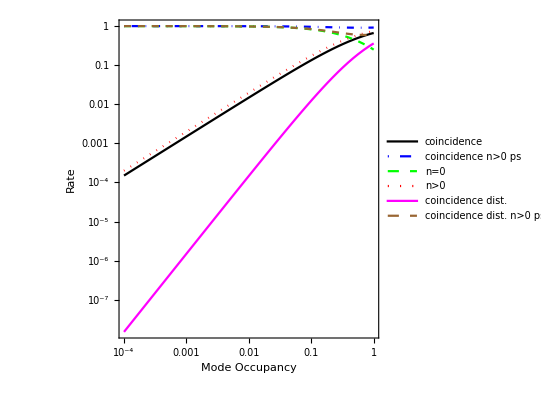

```mathematica
LogLogPlot[{1-ncoProb/.{λ->Abs[lambdaGivenN[x]]},
1-(ncoProb-noProb)/.{λ->Abs[lambdaGivenN[x]]},
noProb/.{λ->Abs[lambdaGivenN[x]]},
1-noProb/.{λ->Abs[lambdaGivenN[x]]},
1-ncoDistProb/.{λ->Abs[lambdaGivenN[x]]},
1-(ncoDistProb-noProb)/.{λ->Abs[lambdaGivenN[x]]}
},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

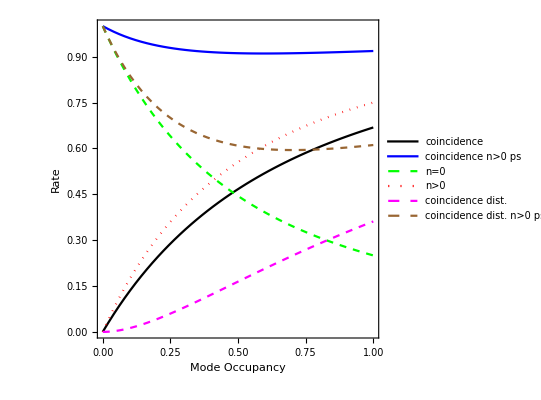

```mathematica
Plot[{1-ncoProb/.{λ->Abs[lambdaGivenN[x]]},
1-(ncoProb-noProb)/.{λ->Abs[lambdaGivenN[x]]},
noProb/.{λ->Abs[lambdaGivenN[x]]},
1-noProb/.{λ->Abs[lambdaGivenN[x]]},
1-ncoDistProb/.{λ->Abs[lambdaGivenN[x]]},
1-(ncoDistProb-noProb)/.{λ->Abs[lambdaGivenN[x]]}
},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue},{Green,Dashed},{Red,Dotted},{Magenta,Dashed},{Brown,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

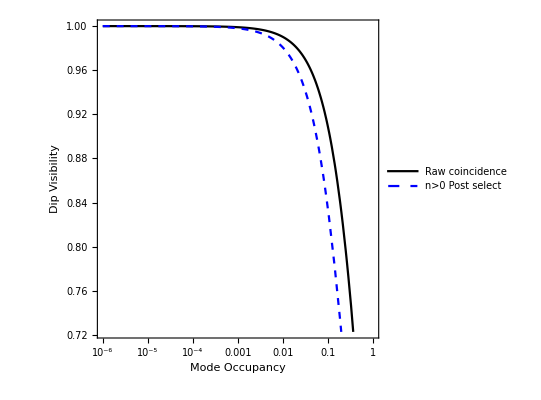

```mathematica
HOMDipVisibility=(-(1-ncoDistProb)+(1-ncoProb) )/(1-ncoProb) ;
HOMDipVisibilityPS=((-(ncoDistProb-noProb))+(1-(ncoProb-noProb)) )/(1-(ncoProb-noProb));
LogLinearPlot[{
HOMDipVisibility/.{λ->Abs[lambdaGivenN[x]]},
HOMDipVisibilityPS/.{λ->Abs[lambdaGivenN[x]]}}
,{x,1,10^-6},AspectRatio->1,PlotLegends->Placed[{"Raw coincidence","n>0 Post select"},Top],PlotStyle->{{Black},{Blue,Dashed},{Green,Dotted},{Red,DotDashed}},Frame->True,FrameLabel->{"Mode Occupancy","Dip Visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

```mathematica
HOMDipVisibility
```

(1-λ^4+((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2))/(1+((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2))

```mathematica
FullSimplify[HOMDipVisibility,Assumptions->{n>0,m>0}]
```

(2-2 λ^2)/(6-6 λ^2+λ^4)

```mathematica
Limit[HOMDipVisibility,λ->0]
```

1/3

```mathematica
(1-ncoDistProb)/.{λ->Abs[lambdaGivenN[0.01]]}
(1-ncoProb) /.{λ->Abs[lambdaGivenN[0.01]]}
HOMDipVisibility/.{λ->Abs[lambdaGivenN[0.1]]}
```

0.000147043

0.0000980296

0.332829

```mathematica
Series[x^y,{x,0}]
```

Series::sspec: Series specification {x,0} is not a list with three elements.

```mathematica
Series[x^y,{y,0,3}]
```

1+Log[x] y+1/2 Log[x]^2 y^2+1/6 Log[x]^3 y^3+O[y]^4

```mathematica
probnm[n_,m_]=((1-λ^2)(λ^(n+m)))^2
probncoNM[n_,m_]=2*(1/2)^(n+m)
probncoNMPiece[n_,m_]=Piecewise[{{2*(1/2)^(n+m),n+m≥ 2}},1]
```

λ^(2 m+2 n) (1-λ^2)^2

2^(1-m-n)

Piecewise[{{2^(1-m-n), m+n≥2}, {1, True}}]

```mathematica
probncoNMPiece[1,0]
```

0

```mathematica
Sum[probnm[n,m],{n,0,∞},{m,0,∞}]
```

1

```mathematica
Expand[Sum[probnm[n,m],{n,1,∞},{m,1,∞}]+probnm[0,0]+probnm[0,1]+Sum[probnm[0,m],{m,2,∞}]+probnm[1,0]+Sum[probnm[n,0],{n,2,∞}]]
```

1

```mathematica
noncodista=FullSimplify[Sum[probnm[n,m]probncoNMPiece[n,m],{n,0,∞},{m,0,∞}],Assumptions->{λ∈Reals,λ>0}]
```

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

```mathematica
noncodistb=FullSimplify[Sum[probnm[n,m]probncoNM[n,m],{n,1,∞},{m,1,∞}]+probnm[0,0]+probnm[0,1]+Sum[probnm[0,m]probncoNM[0,m],{m,2,∞}]+probnm[1,0]+Sum[probnm[n,0]probncoNM[n,0],{n,2,∞}],Assumptions->{λ∈Reals,λ>0}]
```

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

```mathematica
probnm[0,0]
```

(1-λ^2)^2

```mathematica
probnm[1,0]
```

λ^2 (1-λ^2)^2

```mathematica
probnm[0,1]
```

λ^2 (1-λ^2)^2

```mathematica
FullSimplify[Sum[probnm[n,m]probncoNM[n,m],{n,1,∞},{m,1,∞}],Assumptions->{λ∈Reals,λ>0}]
```

(2 λ^4 (-1+λ^2)^2)/((-2+λ^2)^2)

```mathematica
FullSimplify[Sum[probnm[0,m]probncoNM[0,m],{m,2,∞}],Assumptions->{λ∈Reals,λ>0}]
```

-(λ^4 (-1+λ^2)^2)/(-2+λ^2)

```mathematica
FullSimplify[Sum[probnm[n,0]probncoNM[n,0],{n,2,∞}],Assumptions->{λ∈Reals,λ>0}]
```

-(λ^4 (-1+λ^2)^2)/(-2+λ^2)

```mathematica
noncodista/.λ->0.1
noncodistb/.λ->0.1
```

0.99985

0.99985

0.99985

```mathematica
ncoDistProb=noncodista
ncoDistProb/.λ->0.1
```

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

0.99985

```mathematica
FullSimplify[(1-λ^2)^2 Sum[(λ^n)^2 (n+1)2 (1/2)^n,{n,0,∞}]-(1-λ^2)^2]
```

(-1+λ^2)^2 (-1+8/((-2+λ^2)^2))

```mathematica
noDistProb=(1-λ^2)^2
```

(1-λ^2)^2

```mathematica
ncoDistProb/.λ->0.1
```

1.20331

```mathematica
NHeadsChance[n_,h_]=(1/2)^n Binomial[n,h]
```

2^-n Binomial[n,h]

Plot::plln: Limiting value n in {x,0,n} is not a machine-sized real number.

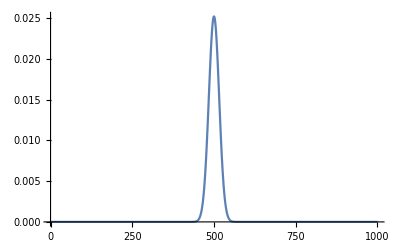

```mathematica
Plot[NHeadsChance[n,x],{x,0,n},PlotRange->All]/.{n->1000}
```

## Postselection

```mathematica
ProbNcoDistNtot=FullSimplify[Sum[probnm[n,m]probncoNM[n,m] KroneckerDelta[n+m-t],{n,1,t},{m,1,t}]+ 2*((1-λ^2)(λ^t))^2 2*(1/2)^t,Assumptions->{λ∈Reals,λ>0,t≥ 2}]
```

2^(1-t) (1+t) λ^(2 t) (-1+λ^2)^2

```mathematica
ProbNcoDistNtot=FullSimplify[Sum[((1-λ^2)(λ^t))^2*2*(1/2)^t,{n,2,t}]+ 2*((1-λ^2)(λ^t))^2 2*(1/2)^t,Assumptions->{λ∈Reals,λ>0,t>0}]
```

2^(1-t) (1+t) λ^(2 t) (-1+λ^2)^2

```mathematica
ProbNcoIndistNtot=2 ( ( 1-λ^2) λ^t)^2
```

2 λ^(2 t) (1-λ^2)^2

```mathematica
visbPostSelNtot=FullSimplify[((1-ProbNcoDistNtot)-(1-ProbNcoIndistNtot))/(1-ProbNcoDistNtot),Assumptions->{λ∈Reals,λ>0,λ<1(*,t>0*)}]
```

-(2 (-1+2^t-t) λ^(2 t) (-1+λ^2)^2)/(-2^t+2 (1+t) λ^(2 t) (-1+λ^2)^2)

```mathematica
visbPostSelNtot/.{t->2,λ->0.5}
```

0.0185567

```mathematica
visbPostSelNtot/.{t->3,λ->Abs[lambdaGivenN[0.9]]}
```

0.0303346

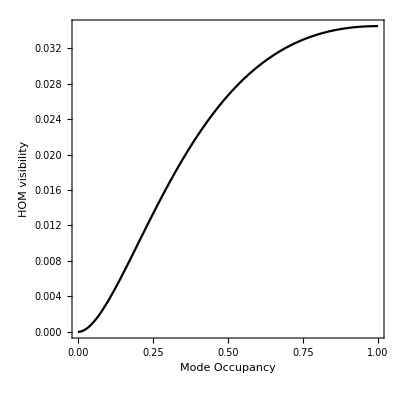

```mathematica
Plot[{visbPostSelNtot/.{λ->Abs[lambdaGivenN[x]],t->2}},{x,1,10^-4},AspectRatio->1,PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","HOM visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```